ω0 = 274.783 rad/s

G = 1524.15

moshil{25.1516,52.1205,771.452}

moshil{34.5791,50.4814,752.258}

moshil{30.2302,77.8786,719.012}

moshil{19.4179,136.255,698.422}

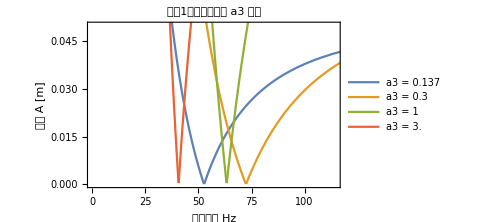

moshil{49.8887,70.6969,771.47}

moshil{35.6197,52.8274,771.456}

moshil{25.1516,52.1205,771.452}

moshil{4.9528,51.6103,771.445}

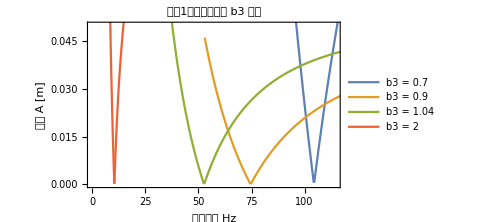

moshil{25.1547,53.0137,725.503}

moshil{24.8216,31.7126,2330.4}

moshil{20.0956,25.8469,4033.23}

moshil{13.7788,25.5493,5955.17}

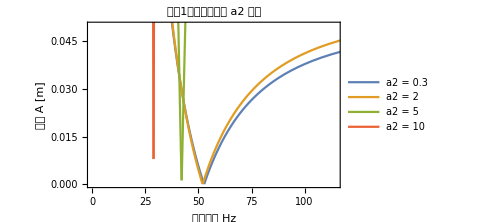

moshil{25.1506,51.82,1007.39}

moshil{25.164,42.0664,60.1389}

moshil{24.0766,25.1706,58.7297}

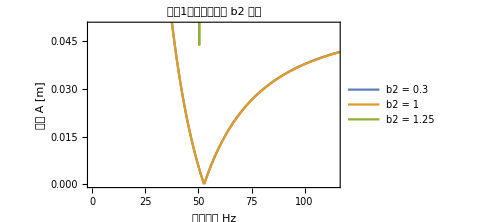

D:\unstable_regions.xlsx

```mathematica
(*清除所有变量*)ClearAll["Global`*"];

(* ==================物理参数（固定）==================*)
l1=0.15;(*杆1长度[m]*)d1=0.006;(*杆1直径[m]*)EE=15.069*10^9;(*弹性模量[Pa]*)ρ=887;(*密度[kg/m^3]*)g=9.800;(*重力加速度[m/s^2]*)ω0=Sqrt[EE*d1^2/(16*ρ*l1^4)];(*参考频率[rad/s]*)G=EE/(4*Pi*ρ^2)(*g/l1;*);
(*无量纲重力项*)Print["ω0 = ",ω0," rad/s"];
Print["G = ",G];

(*阻尼系数（固定）*)
d1d=0.00;d2d=0.00;d3d=0.00;
damping=DiagonalMatrix[{d1d,d2d,d3d}];

(* ==================基准比例参数==================*)
a2base=0.333;b2base=0.333;a3base=0.137;b3base=1.04;

(* ==================定义计算模态1边界的函数==================*)
GetMode1Boundary[{a2_,b2_,a3_,b3_},εlist_]:=Module[{A11,A12,A13,A22,A33,B1,M,K0,K1,vals,vecs,order,ω,vecsSorted,U,Ucol,Cmodal,ζ1,γ1,εvalid,r,Ωminus,Ωplus,A},(*计算常数系数*)A11=1/3+a2 (1-b2+b2^2/3)+a3 (1+b3^2/3);
A12=a2 (b2^2/3-b2/2);
A13=a3 b3^2/3;
A22=a2 b2^2/3;
A33=a3 b3^2/3;
B1=1/2+a2+a3+(a2 b2)/2;
M={{A11,A12,A13},{A12,A22,0},{A13,0,A33}};
K0={{ω0^2-B1 G,-(a2 b2)/2 G,0},{-(a2 b2)/2 G,(a2^2/b2^3) ω0^2-(a2 b2)/2 G,0},{0,0,(a3^2/b3^3) ω0^2}};
K1=(a3 b3)/2*{{1,0,1},{0,0,0},{1,0,1}};
(*模态分析*){vals,vecs}=Eigensystem[{K0,M}];

order=Ordering[vals];

ω=Sqrt[vals[[order]]];
Print["moshil",ω/6.28];
vecsSorted=vecs[[order]];

U=Orthogonalize[vecsSorted,Dot[#1,M.#2]&];
Ucol=Transpose[U];
Cmodal=Transpose[Ucol].damping.Ucol;
ζ1=Cmodal[[1,1]]/(2 ω[[1]]);(*模态1阻尼比*)γ1=Ucol[[All,1]].K1.Ucol[[All,1]];(*耦合系数*)(*过滤 ε 列表，只保留大于阻尼比的值*)εvalid=Select[εlist,#>ζ1&];
If[Length[εvalid]==0,Return[{}]];
r=Sqrt[εvalid^2-ζ1^2];
(*仅保留使 1-2r>0 的点（保证 Ωplus 为正实数）*)validIdx=Flatten[Position[r,_?(#<0.5&)]];
If[Length[validIdx]==0,Return[{}]];
εvalid=εvalid[[validIdx]];
r=r[[validIdx]];
Ωminus=2 ω[[1]]/Sqrt[1+2 r];
Ωplus=2 ω[[1]]/Sqrt[1-2 r];
A=εvalid*l1/Abs[γ1];
{Transpose[{Ωminus,A}],Transpose[{Ωplus,A}]}]

(* ==================绘图参数==================*)
Amax=0.05;(*振幅上限*)Ωrange={0,2.5 ω0};(*频率范围*)εlist=Table[ε,{ε,0.001,0.5,0.01}];(*ε 上限取0.4确保 r<0.5*)(* ==================定义数据块生成函数==================*)MakeBlock[val_,curves_]:=Module[{block},If[curves=={},Return[{}]];
block={};
AppendTo[block,{ToString[val],""}];(*参数值行*)AppendTo[block,{"Left boundary",""}];
AppendTo[block,{"Ω-","A"}];
block=Join[block,curves[[1]]];(*左边界数据*)AppendTo[block,{"",""}];(*空行*)AppendTo[block,{"Right boundary",""}];
AppendTo[block,{"Ω+","A"}];
block=Join[block,curves[[2]]];(*右边界数据*)AppendTo[block,{"",""}];AppendTo[block,{"",""}];(*两个空行分隔*)block]

(* ==================1. a3 变化==================*)a3list={0.137,0.3,1,3.0};
colors=ColorData[97]/@Range[Length[a3list]];
dataA3={};(*改为存储每个a3对应的块*)plot1=Show[Table[Module[{curves},curves=GetMode1Boundary[{a2base,b2base,a3list[[i]],b3base},εlist];
curves=curves/.{x_?NumericQ,y_?NumericQ}:>{x/6,y};
If[curves=!={},AppendTo[dataA3,MakeBlock[a3list[[i]],curves]];(*使用AppendTo存储块*)ListLinePlot[curves,PlotStyle->{colors[[i]],colors[[i]]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],colors[[i]]],PlotLegends->{StringForm["a3 = ``",a3list[[i]]]}],Nothing]],{i,Length[a3list]}],PlotRange->{#/6&/@Ωrange,{0,Amax}},Frame->True,FrameLabel->{"激励频率 Hz","振幅 A [m]"},PlotLabel->"模态1不稳定区域随 a3 变化",ImageSize->Medium]
(*若无数据，放置一个占位块列表*)
If[dataA3=={},dataA3={{{"No data for a3 variation",""}}}];

(* ==================2. b3 变化==================*)
b3list={0.7,0.9,1.04,2};
colors=ColorData[97]/@Range[Length[b3list]];
dataB3={};
plot2=Show[Table[Module[{curves},curves=GetMode1Boundary[{a2base,b2base,a3base,b3list[[i]]},εlist];
curves=curves/.{x_?NumericQ,y_?NumericQ}:>{x/6,y};
If[curves=!={},AppendTo[dataB3,MakeBlock[b3list[[i]],curves]];
ListLinePlot[curves,PlotStyle->{colors[[i]],colors[[i]]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],colors[[i]]],PlotLegends->{StringForm["b3 = ``",b3list[[i]]]}],Nothing]],{i,Length[b3list]}],PlotRange->{#/6&/@Ωrange,{0,Amax}},Frame->True,FrameLabel->{"激励频率 Hz","振幅 A [m]"},PlotLabel->"模态1不稳定区域随 b3 变化",ImageSize->Medium]
If[dataB3=={},dataB3={{{"No data for b3 variation",""}}}];

(* ==================3. a2 变化==================*)
a2list={0.3,2,5,10};
colors=ColorData[97]/@Range[Length[a2list]];
dataA2={};
plot3=Show[Table[Module[{curves},curves=GetMode1Boundary[{a2list[[i]],b2base,a3base,b3base},εlist];
curves=curves/.{x_?NumericQ,y_?NumericQ}:>{x/6,y};
If[curves=!={},AppendTo[dataA2,MakeBlock[a2list[[i]],curves]];
ListLinePlot[curves,PlotStyle->{colors[[i]],colors[[i]]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],colors[[i]]],PlotLegends->{StringForm["a2 = ``",a2list[[i]]]}],Nothing]],{i,Length[a2list]}],PlotRange->{#/6&/@Ωrange,{0,Amax}},Frame->True,FrameLabel->{"激励频率 Hz","振幅 A [m]"},PlotLabel->"模态1不稳定区域随 a2 变化",ImageSize->Medium]
If[dataA2=={},dataA2={{{"No data for a2 variation",""}}}];

(* ==================4. b2 变化==================*)
b2list={0.3,1,1.25};
colors=ColorData[97]/@Range[Length[b2list]];
dataB2={};
plot4=Show[Table[Module[{curves},curves=GetMode1Boundary[{a2base,b2list[[i]],a3base,b3base},εlist];
curves=curves/.{x_?NumericQ,y_?NumericQ}:>{x/6,y};
If[curves=!={},AppendTo[dataB2,MakeBlock[b2list[[i]],curves]];
ListLinePlot[curves,PlotStyle->{colors[[i]],colors[[i]]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],colors[[i]]],PlotLegends->{StringForm["b2 = ``",b2list[[i]]]}],Nothing]],{i,Length[b2list]}],PlotRange->{#/6&/@Ωrange,{0,Amax}},Frame->True,FrameLabel->{"激励频率 Hz","振幅 A [m]"},PlotLabel->"模态1不稳定区域随 b2 变化",ImageSize->Medium]
If[dataB2=={},dataB2={{{"No data for b2 variation",""}}}];

(* ==================定义横向合并函数==================*)
mergeBlocks[blocks_List]:=Module[{maxLen,paddedBlocks,merged},(*如果块列表包含无数据占位符，则直接返回原样*)If[blocks=={{{"No data for a3 variation",""}}}||blocks=={{{"No data for b3 variation",""}}}||blocks=={{{"No data for a2 variation",""}}}||blocks=={{{"No data for b2 variation",""}}},Return[blocks]];
maxLen=Max[Length/@blocks];(*所有块的最大行数*)paddedBlocks=PadRight[#,maxLen,{None,None}]&/@blocks;(*每个块补足行数*)(*将每个块的第 i 行并排排列*)merged=Table[Flatten[Table[paddedBlocks[[j,i]],{j,Length[blocks]}]],{i,maxLen}];
merged]

(* ==================准备导出数据==================*)
exportData={"a3"->mergeBlocks[dataA3],"b3"->mergeBlocks[dataB3],"a2"->mergeBlocks[dataA2],"b2"->mergeBlocks[dataB2]};

(* ==================导出数据到 Excel==================*)
Export["D:\\unstable_regions.xlsx",exportData]
```